```mathematica
Вариант 7
```

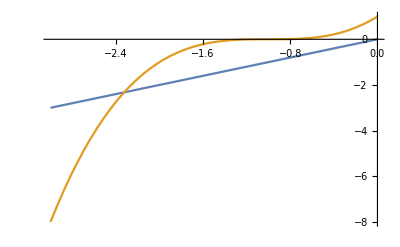

```mathematica
Plot[{x,(x+1)^3},{x,-3,0}]
```

```mathematica
Clear["Global`*"];
f[x_]:=(x+1)^3-x;(*условие*)
φ[x_]:=x+M f[x];(*один из возможных вариантов задания функции φ для метода простых итераций: x=φ(x), 0<φ'(x)<1*)
x0=-2; (*начальное приближение, находим, например, графически*)
ε=0.001;(*точность вычислений: |Subscript[x, точное]-Subscript[x, приближенное]|<ε*)
N[Reduce[0<D[φ[x],x]<1]/.x->x0] (*ищем, какое значение можно взять в качестве M для заданного x0*)
```

-0.5<M<0.

```mathematica
M=-0.25;
Clear[iter,x1,x2]; (*очищаем значения переменных*)
x1=x0; x2=φ[x1];
iter=0;
While[(x2-x1)^2/Abs[2x1-x2-x0]≥ε, (*условие остановки метода, формула со стр.6 лабораторной*)
x0=x1;
x1=x2;
x2=φ[x1];(*метод простых итераций*)
iter++;
If[iter>100,Break[]](*если количество итераций превышает допустимое значение 100, то прекратить вычисления*)]
Print["Метод простых итераций нашел корень x=",N[x2]," при заданной точности ε=",ε,",\nпотребовавшееся количество итераций - ",iter]
```

Метод простых итераций нашел корень x=-2.32475 при заданной точности ε=0.001,
потребовавшееся количество итераций - 2

```mathematica
N[Solve[f[x]==0,x]] (*точные значения корней*)
```

{{x→-2.32472},{x→-0.337641-0.56228 ⅈ},{x→-0.337641+0.56228 ⅈ}}

```mathematica
Вариант 12
```

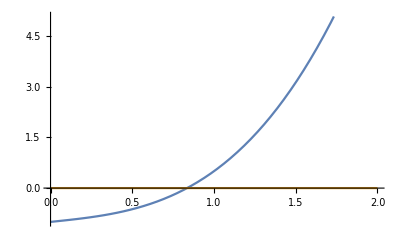

```mathematica
Plot[{x^3+0.5x-1,0},{x,0,2}]
```

```mathematica
Clear["Global`*"];
f[x_]:=x^3+1/2 x-1;(*условие*)
φ[x_]:=x+M f[x];(*один из возможных вариантов задания функции φ для метода простых итераций: x=φ(x), 0<φ'(x)<1*)
x0=0; (*начальное приближение, находим, например, графически*)
ε=0.001;(*точность вычислений: |Subscript[x, точное]-Subscript[x, приближенное]|<ε*)
N[Reduce[0<D[φ[x],x]<1]/.x->x0] (*ищем, какое значение можно взять в качестве M для заданного x0*)
```

-2.<M<0.

```mathematica
M=-0.5;
Clear[iter,x1,x2]; (*очищаем значения переменных*)
x1=x0; x2=φ[x1];
iter=0;
While[(x2-x1)^2/Abs[2x1-x2-x0]≥ε, (*условие остановки метода, формула со стр.6 лабораторной*)
x0=x1;
x1=x2;
x2=φ[x1];(*метод простых итераций*)
iter++;
If[iter>100,Break[]](*если количество итераций превышает допустимое значение 100, то прекратить вычисления*)]
Print["Метод простых итераций нашел корень x=",N[x2]," при заданной точности ε=",ε,",\nпотребовавшееся количество итераций - ",iter]
```

Метод простых итераций нашел корень x=0.835664 при заданной точности ε=0.001,
потребовавшееся количество итераций - 4

```mathematica
N[Solve[f[x]==0,x]] (*точные значения корней*)
```

{{x→0.835122},{x→-0.417561-1.01147 ⅈ},{x→-0.417561+1.01147 ⅈ}}